## Analysis of the SAIR using the RN:

```mathematica
ClearAll["Global‘*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession, NotebookAutoSave -> True];
NotebookSave[];
AppendTo[$Path, FileNameJoin[{$HomeDirectory, "Dropbox", "Codes"}]];
(*SystemOpen[FileNameJoin[{$HomeDirectory, "Kernel", "EpidCRN.m"}]];*)

<<EpidCRN`;
(*?EpidCRN`* *)
Needs["ReactionKinetics`"];

Format[ga]:=γ;Format[be]:=β;Format[mu]:=μ;Format[La]=Λ;
Format[lv]:=Subscript[λ,v]; Format[ln]:=Subscript[λ,n];Format[kvv]:=Subscript[k,vv];
Format[kvn]:=Subscript[k,vn];Format[knn]:=Subscript[k,nn];Format[knv]:=Subscript[k,nv];
Format[iv]:=Subscript[i,v]; Format[in]:=Subscript[i,n];Format[ivv]:=Subscript[i,vv];
Format[ivn]:=Subscript[i,vn];Format[inn]:=Subscript[i,nn];
clm=La->mu;cDFE={iv->0,in->0,ivv->0,ivn->0,inn->0};csi=knv->kvn;ck={knv->k,kvn->k,kvv->k,knn->k};
mR=be/(ga+mu);sd=La/mu;
R0=sd mR;cLa=La->R mu/mR;


(*cai={ai->γa-ar};cga={γa->ai+ar};*) cr={r->1-s-a-i};
RN={"0"->"S","Iv"->"S","In"->"S","Ivv"->"S","Inn"->"S","Ivn"->"S",
(*S >Iv*)"S"+"Iv"-> 2 "Iv", "S"+"Ivv"-> "Iv"+ "Ivv","S"+"Ivn"-> "Iv"+ "Ivn",
(*S >In*) "S"+"In"-> 2 "In", "S"+"Inn"-> "In"+ "Inn","S"+"Ivn"-> "In"+ "Ivn",
(*Iv >Ivv*)2 "Iv"->"Ivv"+"Iv","Ivv"+"Iv"->2 "Ivv","Iv"+"Ivn"->"Ivv"+"Ivn",
(*Iv >Ivn*)2 "Iv"->"Ivn"+"Iv","Iv"+"Ivv"->"Ivn"+"Ivv","Iv"+"Ivn"->2 "Ivn",
(*In >Inn*)2 "In"->"Inn"+"In","In"+"Inn"->2 "Inn","In"+"Ivn"->"Inn"+"Ivn",
(*In >Ivn*)2 "In"->"Ivn"+"In","In"+"Inn"->"Ivn"+"Inn","In"+"Ivn"->2"Ivn",
"Iv"->"0","In"->"0","Ivv"->"0","Inn"->"0","Ivn"->"0","S"->"0"};
var={s,iv,in,ivv,inn,ivn};
RND=ReactionsData[RN];
S= RND["γ"]//Normal;
Print["S",S//MatrixForm]
Print["has ", nR, " cols"]
expo= RND["α"]//Normal//Transpose;
{comp,reac,nR,spec,nS,vol,vars,defi}=RND["complexes","reactionsteps","R","species","M","volpertgraph",
"variables","deficiency"];
rv=expM[var,expo];(*monomial part of rates*)
tra={La  ,ga ,ga ,ga ,ga ,ga,
(*S >Iv*)be,be,be /2,
(*S >In*)be,be,be/2,
(*Iv >Ivv*)be kvv,be kvv,be kvv/2,
(*Iv >Ivn*)be kvn, be kvn,be kvn /2,
(*In >Inn*)be knn,be knn,be knn/2,
(*In >Ivn*)be knv,be knv,be knv/2,
 mu,mu,mu,mu,mu,mu };
Rv=tra*rv;(*/.clm;rates*)
RHS=S.Rv//Simplify; 
 Print["Check sum ",Total[RHS]//FullSimplify]
par=Par[RHS,var];cp=Append[Thread[par>0],γa>0];
Print["GM model  ",RHS//MatrixForm," has ", par//Length,
" par : ", par];cp=Thread[par>0];
$Assumptions=cp;
fl=cons[S//Transpose]//Transpose;
Print["The GM has rank ",MatrixRank[S],
"  deficiency ", defi, 
" and ",comp//Length," complexes and ",fl//Length,"  fluxes"]
Timing[so=Solve[(RHS/.ck/.cLa)==0,var]//FullSimplify;]
Print["The  ", so//Length,"fixed points are"]
so
```

S(1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | -1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | -1 | 0)

has30 cols

Check sum Λ-μ (i_n+i_nn+i_v+i_vn+i_vv+s)

GM model  (γ (i_n+i_nn+i_v+i_vn+i_vv)+Λ-(β (i_n+i_nn+i_v+i_vn+i_vv)+μ) s
-γ i_v-i_v μ-1/2 β (2 i_v+i_vn+2 i_vv) (i_v (k_vn+k_vv)-s)
-γ i_n-i_n μ-1/2 β (2 i_n+2 i_nn+i_vn) (i_n (k_nn+k_nv)-s)
-γ i_vv+1/2 β i_v (2 i_v+i_vn+2 i_vv) k_vv-i_vv μ
-γ i_nn+1/2 β i_n (2 i_n+2 i_nn+i_vn) k_nn-i_nn μ
-γ i_vn+1/2 β (2 i_n^2 k_nv+i_n (2 i_nn+i_vn) k_nv+i_v (2 i_v+i_vn+2 i_vv) k_vn)-i_vn μ) has 8 par : {β,γ,k_nn,k_nv,k_vn,k_vv,Λ,μ}

The GM has rank 6  deficiency δ=N-L-S=23-2-6=15 and 23 complexes and 30  fluxes

{44.7656,Null}

The  6fixed points are

{{s→((γ+μ) R)/β,i_v→0,i_n→0,i_vv→0,i_nn→0,i_vn→0},{s→(γ+μ)/β,i_v→((γ+μ) (-1+R))/(2 (β+β k (-1+R))),i_n→((γ+μ) (-1+R))/(2 (β+β k (-1+R))),i_vv→(k (γ+μ) (-1+R)^2)/(4 (β+β k (-1+R))),i_nn→(k (γ+μ) (-1+R)^2)/(4 (β+β k (-1+R))),i_vn→(k (γ+μ) (-1+R)^2)/(2 (β+β k (-1+R)))},{s→(γ+μ)/β,i_v→((γ+μ) (k+√(k (2+k (-1+R)) (-1+R))-k R))/(2 β k),i_n→-((γ+μ) (k (-1+R)+√(k (2+k (-1+R)) (-1+R))))/(2 β k),i_vv→((γ+μ) (-1+R))/(2 β),i_nn→((γ+μ) (-1+R))/(2 β),i_vn→((γ+μ) (-1+R))/β},{s→(γ+μ)/β,i_v→-((γ+μ) (k (-1+R)+√(k (2+k (-1+R)) (-1+R))))/(2 β k),i_n→((γ+μ) (k+√(k (2+k (-1+R)) (-1+R))-k R))/(2 β k),i_vv→((γ+μ) (-1+R))/(2 β),i_nn→((γ+μ) (-1+R))/(2 β),i_vn→((γ+μ) (-1+R))/β},{s→((γ+μ) R)/β,i_v→((γ+μ) (2 k (-1+R)+√2 √(k^2 (-2+R) (-1+R))))/(2 β k^2),i_n→-((γ+μ) (-2 k (-1+R)+√2 √(k^2 (-2+R) (-1+R))))/(2 β k^2),i_vv→-((γ+μ) (k (-2+R)+√2 √(k^2 (-2+R) (-1+R))) (-1+R))/(2 β k^2 (-2+R)),i_nn→((γ+μ) (-k (-2+R)+√2 √(k^2 (-2+R) (-1+R))) (-1+R))/(2 β k^2 (-2+R)),i_vn→-((γ+μ) (-1+R))/(β k)},{s→((γ+μ) R)/β,i_v→((γ+μ) (2 k (-1+R)-√2 √(k^2 (-2+R) (-1+R))))/(2 β k^2),i_n→((γ+μ) (2 k (-1+R)+√2 √(k^2 (-2+R) (-1+R))))/(2 β k^2),i_vv→((γ+μ) (-k (-2+R)+√2 √(k^2 (-2+R) (-1+R))) (-1+R))/(2 β k^2 (-2+R)),i_nn→-((γ+μ) (k (-2+R)+√2 √(k^2 (-2+R) (-1+R))) (-1+R))/(2 β k^2 (-2+R)),i_vn→-((γ+μ) (-1+R))/(β k)}}

```mathematica
I1=iv+in/.so[[2]]//FullSimplify
I2=ivv+ivn+inn/.so[[2]]//FullSimplify
```

((γ+μ) (-1+R))/(β+β k (-1+R))

(k (γ+μ) (-1+R)^2)/(β+β k (-1+R))

```mathematica
I1=iv+in/.so[[3]]//FullSimplify
I2=ivv+ivn+inn/.so[[3]]//FullSimplify

I1=iv+in/.so[[6]]//FullSimplify
I2=ivv+ivn+inn/.so[[6]]//FullSimplify
```

-((γ+μ) (-1+R))/β

(2 (γ+μ) (-1+R))/β

(2 (γ+μ) (-1+R))/(β k)

-(2 (γ+μ) (-1+R))/(β k)

```mathematica
I1=iv+in/.so[[4]]//FullSimplify
I2=ivv+ivn+inn/.so[[4]]//FullSimplify

I1=iv+in/.so[[5]]//FullSimplify
I2=ivv+ivn+inn/.so[[5]]//FullSimplify
```

-((γ+μ) (-1+R))/β

(2 (γ+μ) (-1+R))/β

(2 (γ+μ) (-1+R))/(β k)

-(2 (γ+μ) (-1+R))/(β k)

```mathematica
jac=Grad[RHS,var]//FullSimplify;
chEq=CharacteristicPolynomial[jac,u]//Factor;
chE= chEq/.so[[1]]//Factor;
ch0= chEq/.so[[2]]//Factor;
Print["Jacobian at DFE",jac/.cDFE//MatrixForm," does not have block form, but chEq has two trivial 
factors ",chEq/.cDFE//Factor]
```

### Computation of Jy, its principal eigenvectors, and R0 using NGM script, and the check of the positivity of the endemic point:

```mathematica
mod={RHS,var,par};
inf={2,3};
Print["(a'
i')=", RHS[[inf]]//MatrixForm]
xv=var[[inf]];cv=Thread[xv>0];
jacI=Grad[RHS[[inf]],xv]; 
ng=NGM[mod,inf];Kl=ng[[6]];K=ng[[7]];M=ng[[1]];
Tm=ng[[5]];
F=ng[[4]];
Print["M is",M//MatrixForm, " F=",F,"  Kl=",Kl//MatrixForm," and K=",K//MatrixForm," has eigval"]
eig=K//Eigenvalues
{eval, evec} = Eigensystem[F];
(*Transpose[evec] . DiagonalMatrix[eval] . Inverse[Transpose[evec]]//MatrixForm*)

Print["eval is ",la=eval[[2]]," right and left principal eigvecs of F are",
va=evec[[2]],bb= la Inverse[Transpose[evec]][[2]]/s]
Fp= Outer[Times,va,bb];
Print["Check F",Fp//MatrixForm]
R0=eig[[2]]/.cDFE//FullSimplify;
Print["R0=",R0," for Ott1=",R0/.cO1," for Ott2=",R0/.cO2//Simplify]
reiv=Inverse[-Tm].va//FullSimplify;
leiv=bb.Inverse[-Tm]//FullSimplify;

Print["A=",Tm//MatrixForm,"dwell times=",reiv,"C=leiv=",leiv]
Print["check:M .dwell(leiv) are",M.reiv/.s->1/mR//Factor,leiv.M/.s->1/mR//Factor]
```

(a'
i')=(β_i i s-a (a_i+a_r-β_a s+μ)
a a_i-i (γ_i+δ+μ))

M is(-a_i-a_r+β_a s-μ | β_i s
a_i | -γ_i-δ-μ) F={{β_a s,β_i s},{0,0}}  Kl=((s (a_i β_i+β_a (γ_i+δ+μ)))/((a_i+a_r+μ) (γ_i+δ+μ)) | (β_i s)/(γ_i+δ+μ)
0 | 0) and K=((β_a s)/(a_i+a_r+μ) | (β_i s)/(a_i+a_r+μ)
(a_i β_a s)/((a_i+a_r+μ) (γ_i+δ+μ)) | (a_i β_i s)/((a_i+a_r+μ) (γ_i+δ+μ))) has eigval

{0,(s (a_i β_i+β_a γ_i+β_a δ+β_a μ))/((a_i+a_r+μ) (γ_i+δ+μ))}

eval is β_a s right and left principal eigvecs of F are{1,0}{β_a,β_i}

Check F(β_a | β_i
0 | 0)

R0=(Λ (γ_r+μ) (a_i β_i+β_a (γ_i+δ+μ)))/(μ (a_i+a_r+μ) (γ_r+γ_s+μ) (γ_i+δ+μ)) for Ott1=(μ (a_i β_i+β_a (γ_i+μ)))/((a_i+a_r+μ) (γ_i+μ) (γ_s+μ)) for Ott2=(β (a_i+γ+μ) (γ_r+μ))/((a_i+a_r+μ) (γ+μ) (γ_r+γ_s+μ))

A=(-a_i-a_r-μ | 0
a_i | -γ_i-δ-μ)dwell times={1/(a_i+a_r+μ),a_i/((a_i+a_r+μ) (γ_i+δ+μ))}C=leiv={(a_i β_i+β_a (γ_i+δ+μ))/((a_i+a_r+μ) (γ_i+δ+μ)),β_i/(γ_i+δ+μ)}

check:M .dwell(leiv) are{0,0}{0,0}

```mathematica
jacE=(jacI/.s->1/mR)//FullSimplify;
eigE=Eigenvalues[jacE]//FullSimplify;
Print["infectious Jacobian at EE:",jacE//MatrixForm, "  its eigs are",  eigE]
aH=va .Inverse[s IdentityMatrix[2]+Transpose[ng[[5]]]].bb;
Print["The LT of the total force of infection  is â(s)=", aH, " and R =â(0)=", aH/.s->0//FullSimplify]
xe=xv/.cEE//FullSimplify;ae=xe[[1]];ie=xe[[2]];rE=r/.cEE/.car//FullSimplify;
Print["The quotient of endemic a*/i* is ", aovi=ae/ie//FullSimplify]
Print["The constant"]
ka=mR *ae/((R0-1)reiv[[1]])//FullSimplify;
ki=mR *ie/((R0-1) reiv[[2]])//FullSimplify;
ka==ki
km=ka/.car//FullSimplify;
knn=(kn mR /(R0-1)/.car)//FullSimplify;
{km,knn}
{km,knn}/.cgr
```

infectious Jacobian at EE:(-(a_i β_i (a_i+a_r+μ))/(a_i β_i+β_a (γ_i+δ+μ)) | (β_i (a_i+a_r+μ) (γ_i+δ+μ))/(a_i β_i+β_a (γ_i+δ+μ))
a_i | -γ_i-δ-μ)  its eigs are{0,-(a_i^2 β_i+β_a (γ_i+δ+μ)^2+a_i β_i (a_r+γ_i+δ+2 μ))/(a_i β_i+β_a (γ_i+δ+μ))}

The LT of the total force of infection  is â(s)=β_a/(-a_i-a_r+s-μ)-(a_i β_i)/((-a_i-a_r+s-μ) (s-γ_i-δ-μ)) and R =â(0)=-(a_i β_i+β_a (γ_i+δ+μ))/((a_i+a_r+μ) (γ_i+δ+μ))

The quotient of endemic a*/i* is (γ_i+δ+μ)/a_i

The constant

True

{(μ (γ_a+μ) (γ_r+γ_s+μ) (γ_i+δ+μ))/(a_i γ_r (δ+μ)+μ (γ_a+γ_r+μ) (γ_i+δ+μ)),γ_s+μ}

{γ_s+μ,γ_s+μ}

```mathematica
cp
nE=Numerator[rE]/.cde//FullSimplify
nE//Length
coE=CoefficientList[nE,ai]//FullSimplify
coEd=coE/.cde//FullSimplify
re=Reduce[Append[cp,nE>0&&R0>1]]//FullSimplify
re//Length
```

{a_i>0,a_r>0,β_a>0,β_i>0,Λ>0,γ_i>0,γ_r>0,γ_s>0,δ>0,μ>0}

-a_i^2 β_i Λ μ+(γ_i+μ)^2 (β_a Λ γ_a-(γ_a-γ_s) μ (γ_a+μ))+a_i (γ_i+μ) (β_i Λ γ_a-β_a Λ μ+μ (γ_a+μ) (γ_s+μ))

3

{(γ_i+μ)^2 (β_a Λ γ_a-(γ_a-γ_s) μ (γ_a+μ)),(γ_i+μ) (β_i Λ γ_a-β_a Λ μ+μ (γ_a+μ) (γ_s+μ)),-β_i Λ μ}

{(γ_i+μ)^2 (β_a Λ γ_a-(γ_a-γ_s) μ (γ_a+μ)),(γ_i+μ) (β_i Λ γ_a-β_a Λ μ+μ (γ_a+μ) (γ_s+μ)),-β_i Λ μ}

(γ_i+δ+μ) (-β_a Λ (γ_r+μ)+μ (a_r+μ) (γ_r+γ_s+μ))+a_i (-β_i Λ (γ_r+μ)+μ (γ_r+γ_s+μ) (γ_i+δ+μ))<0&&μ (2 γ_a+μ) (γ_i+μ)<a_i β_i Λ+a_i μ (γ_s+μ)+(γ_i+μ) (β_a Λ+γ_s μ)+√((γ_i+μ)^2 (β_a^2 Λ^2+2 β_a Λ (γ_s-μ) μ+μ^2 (γ_s+μ)^2)+a_i^2 (β_i^2 Λ^2+2 β_i Λ (γ_s-μ) μ+μ^2 (γ_s+μ)^2)+2 a_i (γ_i+μ) (β_a Λ (β_i Λ+(γ_s-μ) μ)+μ (β_i Λ (γ_s-μ)+μ (γ_s+μ)^2)))&&(γ_i+μ) (β_a Λ+(-2 γ_a+γ_s-μ) μ)+a_i (β_i Λ+μ (γ_s+μ))<√((γ_i+μ)^2 (β_a^2 Λ^2+2 β_a Λ (γ_s-μ) μ+μ^2 (γ_s+μ)^2)+a_i^2 (β_i^2 Λ^2+2 β_i Λ (γ_s-μ) μ+μ^2 (γ_s+μ)^2)+2 a_i (γ_i+μ) (β_a Λ (β_i Λ+(γ_s-μ) μ)+μ (β_i Λ (γ_s-μ)+μ (γ_s+μ)^2)))&&((β_a Λ<μ (a_i+μ)&&((((γ_i+μ) (-β_a Λ+μ (a_i+μ))<a_i β_i Λ||β_i>((γ_i+μ) (-β_a Λ+(a_i+μ) (γ_s+μ)))/(a_i Λ))&&(-β_a Λ+μ (a_i+μ)) (a_i β_i Λ-a_i μ (γ_i+δ+μ)+(γ_i+δ+μ) (β_a Λ-μ^2))>0&&((a_i β_i Λ)/(-β_a Λ+(a_i+μ) (γ_s+μ))<γ_i+δ+μ||β_i≤((γ_i+μ) (-β_a Λ+(a_i+μ) (γ_s+μ)))/(a_i Λ))&&γ_r>(μ ((γ_i+δ+μ) (-β_a Λ+μ (γ_s+μ))+a_i (-β_i Λ+(γ_s+μ) (γ_i+δ+μ))))/(a_i β_i Λ-a_i μ (γ_i+δ+μ)+(γ_i+δ+μ) (β_a Λ-μ^2)))||(β_i>((γ_i+μ) (-β_a Λ+(a_i+μ) (γ_s+μ)))/(a_i Λ)&&γ_i+δ+μ≤(a_i β_i Λ)/(-β_a Λ+(a_i+μ) (γ_s+μ)))))||β_a Λ≥(a_i+μ) (γ_s+μ)||(μ (a_i+μ)≤β_a Λ&&((β_i>((γ_i+μ) (-β_a Λ+(a_i+μ) (γ_s+μ)))/(a_i Λ)&&γ_i+δ+μ≤(a_i β_i Λ)/(-β_a Λ+(a_i+μ) (γ_s+μ)))||γ_r>(μ ((γ_i+δ+μ) (-β_a Λ+μ (γ_s+μ))+a_i (-β_i Λ+(γ_s+μ) (γ_i+δ+μ))))/(a_i β_i Λ-a_i μ (γ_i+δ+μ)+(γ_i+δ+μ) (β_a Λ-μ^2)))))

4

```mathematica
re[[1]]
```

(γ_i+δ+μ) (-β_a Λ (γ_r+μ)+μ (a_r+μ) (γ_r+γ_s+μ))+a_i (-β_i Λ (γ_r+μ)+μ (γ_r+γ_s+μ) (γ_i+δ+μ))<0

```mathematica
re[[3]]
```

Λ≥((a_i+μ) (γ_s+μ) (γ_i+δ+μ))/(a_i β_i+β_a (γ_i+δ+μ))||((μ (a_i+μ) (γ_i+δ+μ))/(a_i β_i+β_a (γ_i+δ+μ))<Λ&&γ_r>(μ ((γ_i+δ+μ) (-β_a Λ+μ (γ_s+μ))+a_i (-β_i Λ+(γ_s+μ) (γ_i+δ+μ))))/(a_i β_i Λ-a_i μ (γ_i+δ+μ)+(γ_i+δ+μ) (β_a Λ-μ^2)))

```mathematica
(*Lyapunov*)ct=Join[cp,cv];
di=DiagonalMatrix[xe/xv]//Factor;di//MatrixForm
Print["Lf form",Lfp=leiv.di.(M/.s->1/mR).xv//Factor]
Timing[re=Reduce[Append[ct,Lfp>0],xv]//FullSimplify]
```

(-((γ_i+δ+μ) (-a_i β_i Λ γ_r-β_a Λ γ_i γ_r-β_a Λ γ_r δ-a_i β_i Λ μ-β_a Λ γ_i μ-β_a Λ γ_r μ+a_i γ_i γ_r μ+a_r γ_i γ_r μ+a_i γ_i γ_s μ+a_r γ_i γ_s μ-β_a Λ δ μ+a_i γ_r δ μ+a_r γ_r δ μ+a_i γ_s δ μ+a_r γ_s δ μ-β_a Λ μ^2+a_i γ_i μ^2+a_r γ_i μ^2+a_i γ_r μ^2+a_r γ_r μ^2+γ_i γ_r μ^2+a_i γ_s μ^2+a_r γ_s μ^2+γ_i γ_s μ^2+a_i δ μ^2+a_r δ μ^2+γ_r δ μ^2+γ_s δ μ^2+a_i μ^3+a_r μ^3+γ_i μ^3+γ_r μ^3+γ_s μ^3+δ μ^3+μ^4))/(a (a_i β_i+β_a γ_i+β_a δ+β_a μ) (a_i γ_r δ+a_i γ_i μ+a_r γ_i μ+a_i γ_r μ+γ_i γ_r μ+a_i δ μ+a_r δ μ+γ_r δ μ+a_i μ^2+a_r μ^2+γ_i μ^2+γ_r μ^2+δ μ^2+μ^3)) | 0
0 | (a_i (a_i β_i Λ γ_r+β_a Λ γ_i γ_r+β_a Λ γ_r δ+a_i β_i Λ μ+β_a Λ γ_i μ+β_a Λ γ_r μ-a_i γ_i γ_r μ-a_r γ_i γ_r μ-a_i γ_i γ_s μ-a_r γ_i γ_s μ+β_a Λ δ μ-a_i γ_r δ μ-a_r γ_r δ μ-a_i γ_s δ μ-a_r γ_s δ μ+β_a Λ μ^2-a_i γ_i μ^2-a_r γ_i μ^2-a_i γ_r μ^2-a_r γ_r μ^2-γ_i γ_r μ^2-a_i γ_s μ^2-a_r γ_s μ^2-γ_i γ_s μ^2-a_i δ μ^2-a_r δ μ^2-γ_r δ μ^2-γ_s δ μ^2-a_i μ^3-a_r μ^3-γ_i μ^3-γ_r μ^3-γ_s μ^3-δ μ^3-μ^4))/(i (a_i β_i+β_a γ_i+β_a δ+β_a μ) (a_i γ_r δ+a_i γ_i μ+a_r γ_i μ+a_i γ_r μ+γ_i γ_r μ+a_i δ μ+a_r δ μ+γ_r δ μ+a_i μ^2+a_r μ^2+γ_i μ^2+γ_r μ^2+δ μ^2+μ^3)))

Lf form((β_i (-a a_i+i γ_i+i δ+i μ)^2 (a_i β_i Λ γ_r+β_a Λ γ_i γ_r+β_a Λ γ_r δ+a_i β_i Λ μ+β_a Λ γ_i μ+β_a Λ γ_r μ-a_i γ_i γ_r μ-a_r γ_i γ_r μ-a_i γ_i γ_s μ-a_r γ_i γ_s μ+β_a Λ δ μ-a_i γ_r δ μ-a_r γ_r δ μ-a_i γ_s δ μ-a_r γ_s δ μ+β_a Λ μ^2-a_i γ_i μ^2-a_r γ_i μ^2-a_i γ_r μ^2-a_r γ_r μ^2-γ_i γ_r μ^2-a_i γ_s μ^2-a_r γ_s μ^2-γ_i γ_s μ^2-a_i δ μ^2-a_r δ μ^2-γ_r δ μ^2-γ_s δ μ^2-a_i μ^3-a_r μ^3-γ_i μ^3-γ_r μ^3-γ_s μ^3-δ μ^3-μ^4))/(a i (γ_i+δ+μ) (a_i β_i+β_a γ_i+β_a δ+β_a μ) (a_i γ_r δ+a_i γ_i μ+a_r γ_i μ+a_i γ_r μ+γ_i γ_r μ+a_i δ μ+a_r δ μ+γ_r δ μ+a_i μ^2+a_r μ^2+γ_i μ^2+γ_r μ^2+δ μ^2+μ^3)))

{0.375,(β_i Λ (γ_r+μ)<μ (γ_r+γ_s+μ) (γ_i+δ+μ)&&β_a Λ (γ_r+μ)>μ^2 (γ_r+γ_s+μ)&&μ (a_r+μ) (γ_r+γ_s+μ)<β_a Λ (γ_r+μ)&&a_i<((γ_i+δ+μ) (-β_a Λ (γ_r+μ)+μ (a_r+μ) (γ_r+γ_s+μ)))/(β_i Λ (γ_r+μ)-μ (γ_r+γ_s+μ) (γ_i+δ+μ))&&a>0&&(0<i<(a a_i)/(γ_i+δ+μ)||i (γ_i+δ+μ)>a a_i))||(β_i Λ (γ_r+μ)==μ (γ_r+γ_s+μ) (γ_i+δ+μ)&&β_a Λ (γ_r+μ)>μ^2 (γ_r+γ_s+μ)&&μ (a_r+μ) (γ_r+γ_s+μ)<β_a Λ (γ_r+μ)&&a>0&&(0<i<(a a_i)/(γ_i+δ+μ)||i (γ_i+δ+μ)>a a_i))||(β_i Λ (γ_r+μ)>μ (γ_r+γ_s+μ) (γ_i+δ+μ)&&(0<i<(a a_i)/(γ_i+δ+μ)||i (γ_i+δ+μ)>a a_i)&&a>0&&(a_i>((γ_i+δ+μ) (-β_a Λ (γ_r+μ)+μ (a_r+μ) (γ_r+γ_s+μ)))/(β_i Λ (γ_r+μ)-μ (γ_r+γ_s+μ) (γ_i+δ+μ))||β_a Λ (γ_r+μ)>μ^2 (γ_r+γ_s+μ))&&(a_i>((γ_i+δ+μ) (-β_a Λ (γ_r+μ)+μ (a_r+μ) (γ_r+γ_s+μ)))/(β_i Λ (γ_r+μ)-μ (γ_r+γ_s+μ) (γ_i+δ+μ))||μ (a_r+μ) (γ_r+γ_s+μ)≤β_a Λ (γ_r+μ)))}

```mathematica
re//Length
re[[1]]
re[[2]]
re[[3]]
```

3

β_i Λ (γ_r+μ)<μ (γ_r+γ_s+μ) (γ_i+δ+μ)&&β_a Λ (γ_r+μ)>μ^2 (γ_r+γ_s+μ)&&μ (a_r+μ) (γ_r+γ_s+μ)<β_a Λ (γ_r+μ)&&a_i<((γ_i+δ+μ) (-β_a Λ (γ_r+μ)+μ (a_r+μ) (γ_r+γ_s+μ)))/(β_i Λ (γ_r+μ)-μ (γ_r+γ_s+μ) (γ_i+δ+μ))&&a>0&&(0<i<(a a_i)/(γ_i+δ+μ)||i (γ_i+δ+μ)>a a_i)

β_i Λ (γ_r+μ)==μ (γ_r+γ_s+μ) (γ_i+δ+μ)&&β_a Λ (γ_r+μ)>μ^2 (γ_r+γ_s+μ)&&μ (a_r+μ) (γ_r+γ_s+μ)<β_a Λ (γ_r+μ)&&a>0&&(0<i<(a a_i)/(γ_i+δ+μ)||i (γ_i+δ+μ)>a a_i)

β_i Λ (γ_r+μ)>μ (γ_r+γ_s+μ) (γ_i+δ+μ)&&(0<i<(a a_i)/(γ_i+δ+μ)||i (γ_i+δ+μ)>a a_i)&&a>0&&(a_i>((γ_i+δ+μ) (-β_a Λ (γ_r+μ)+μ (a_r+μ) (γ_r+γ_s+μ)))/(β_i Λ (γ_r+μ)-μ (γ_r+γ_s+μ) (γ_i+δ+μ))||β_a Λ (γ_r+μ)>μ^2 (γ_r+γ_s+μ))&&(a_i>((γ_i+δ+μ) (-β_a Λ (γ_r+μ)+μ (a_r+μ) (γ_r+γ_s+μ)))/(β_i Λ (γ_r+μ)-μ (γ_r+γ_s+μ) (γ_i+δ+μ))||μ (a_r+μ) (γ_r+γ_s+μ)≤β_a Λ (γ_r+μ))

```mathematica
cDFE/.csi
regr=DeleteCases[re/.cO1//FullSimplify,_Symbol>0]
regr//Length
```

{s→Λ/(γ_s+μ),a→0,i→0,r→(Λ γ_s)/(μ (γ_s+μ))}

(β_i μ<(γ_i+μ) (γ_s+μ)&&β_a>γ_s+μ&&μ (a_r+μ) (γ_s+μ)<β_a μ^2&&a_i<((γ_i+μ) (-β_a μ+(a_r+μ) (γ_s+μ)))/(β_i μ-(γ_i+μ) (γ_s+μ))&&a>0&&(0<i<(a a_i)/(γ_i+μ)||i (γ_i+μ)>a a_i))||(β_i μ==(γ_i+μ) (γ_s+μ)&&β_a>γ_s+μ&&μ (a_r+μ) (γ_s+μ)<β_a μ^2&&a>0&&(0<i<(a a_i)/(γ_i+μ)||i (γ_i+μ)>a a_i))||(β_i μ>(γ_i+μ) (γ_s+μ)&&(0<i<(a a_i)/(γ_i+μ)||i (γ_i+μ)>a a_i)&&a>0&&(a_i>((γ_i+μ) (-β_a μ+(a_r+μ) (γ_s+μ)))/(β_i μ-(γ_i+μ) (γ_s+μ))||β_a>γ_s+μ)&&(a_i>((γ_i+μ) (-β_a μ+(a_r+μ) (γ_s+μ)))/(β_i μ-(γ_i+μ) (γ_s+μ))||μ (a_r+μ) (γ_s+μ)≤β_a μ^2))

3

```mathematica
(*Total and Lie derivative *)
 Lf=leiv.{a-ae Log[a],i-ie Log[a]}/.s->1/mR;
Td=Dt[Lf, t, Constants -> par];(*Total  derivative *)
rules = {Dt[a,t,Constants->par] -> RHS[[2]], Dt[i,t,Constants->par] ->RHS[[3]]};
Ld=Td//.rules//.s->1/mR//Factor
R0
```

-((β_i μ (-a a_i+i γ_i+i δ+i μ) (a_i^2 β_i+a_i a_r β_i+a_i β_i γ_i+β_a γ_i^2+a_i β_i δ+2 β_a γ_i δ+β_a δ^2+2 a_i β_i μ+2 β_a γ_i μ+2 β_a δ μ+β_a μ^2) (a_i β_i γ_r-a_i γ_i γ_r-a_r γ_i γ_r+β_a γ_i γ_r-a_i γ_i γ_s-a_r γ_i γ_s-a_i γ_r δ-a_r γ_r δ+β_a γ_r δ-a_i γ_s δ-a_r γ_s δ+a_i β_i μ-a_i γ_i μ-a_r γ_i μ+β_a γ_i μ-a_i γ_r μ-a_r γ_r μ+β_a γ_r μ-γ_i γ_r μ-a_i γ_s μ-a_r γ_s μ-γ_i γ_s μ-a_i δ μ-a_r δ μ+β_a δ μ-γ_r δ μ-γ_s δ μ-a_i μ^2-a_r μ^2+β_a μ^2-γ_i μ^2-γ_r μ^2-γ_s μ^2-δ μ^2-μ^3))/(a (γ_i+δ+μ) (a_i β_i+β_a γ_i+β_a δ+β_a μ)^2 (a_i γ_r δ+a_i γ_i μ+a_r γ_i μ+a_i γ_r μ+γ_i γ_r μ+a_i δ μ+a_r δ μ+γ_r δ μ+a_i μ^2+a_r μ^2+γ_i μ^2+γ_r μ^2+δ μ^2+μ^3)))

((γ_r+μ) (a_i β_i+β_a (γ_i+δ+μ)))/((a_i+a_r+μ) (γ_r+γ_s+μ) (γ_i+δ+μ))

```mathematica
nLd=Numerator[Ld];nLd//Length
va=Variables[nLd]
Exponent[nLd,va]
Exponent[nLd,{a,i}]
fi=FindInstance[Append[Join[cp,{a>0,i>0,R0>1}],nLd>0],va]
nLd/.fi//N
```

6

{bi,μ,a,ai,i,γi,δ,ar,ba,γr,γs}

{3,7,1,4,1,4,4,2,2,1,1}

{1,1}

{{bi→11,μ→1,a→4,ai→1,i→1,γi→1,δ→1,ar→1,ba→1,γr→1,γs→1}}

{825.}

```mathematica
Jdd=Numerator[Together[Det[jac/.dfe]]//FullSimplify];Print["Det[jac/.dfe]=", Jdd]
Print["Det[M/.dfe]=", Det[M/.dfe]//FullSimplify]
Jed=Numerator[Together[Det[jac/.so[[2]]]]]//FullSimplify;
Print["Det[jac/.E*]=", Jed]
rd=Reduce[Append[cp,Jdd==0]]//FullSimplify
re=Reduce[Append[cp,Jed==0]]//FullSimplify
Print["Jed and Jdd are opposites, their sum is"]
Jdd+Jed
(*Print["Det[M/.E*]=", Det[M/.so[[2]]]//FullSimplify]

Print["eigenvalues of M at endemic point are ", Eigenvalues[M/.so[[2]]]//FullSimplify]
Print["eigenvalues of M at E0 are ", Eigenvalues[M/.dfe]//FullSimplify]*)
```

Det[jac/.dfe]=μ ((γ_i+μ) (-β_a (γ_r+μ)+a_r (γ_r+γ_s+μ)+μ (γ_r+γ_s+μ))+a_i (-β_i (γ_r+μ)+(γ_i+μ) (γ_r+γ_s+μ)))

Det[M/.dfe]=((γ_i+μ) (-β_a (γ_r+μ)+a_r (γ_r+γ_s+μ)+μ (γ_r+γ_s+μ))+a_i (-β_i (γ_r+μ)+(γ_i+μ) (γ_r+γ_s+μ)))/(γ_r+γ_s+μ)

Det[jac/.E*]=-μ ((γ_i+μ) (-β_a (γ_r+μ)+a_r (γ_r+γ_s+μ)+μ (γ_r+γ_s+μ))+a_i (-β_i (γ_r+μ)+(γ_i+μ) (γ_r+γ_s+μ)))

```mathematica
(ai>0&&Subscript[γ, r]>0&&γs>0&&μ>0&&ba>(μ (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ar+μ==(ba (Subscript[γ, r]+μ))/(Subscript[γ, r]+γs+μ)&&γi>0&&bi==((γi+μ) (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ))||(μ>0&&Subscript[γ, r]>0&&γs>0&&γi>0&&((0<bi<((γi+μ) (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ba>(μ (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ar>0&&ar+μ<(ba (Subscript[γ, r]+μ))/(Subscript[γ, r]+γs+μ))||(bi>((γi+μ) (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&((0<ba≤(μ (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ar>0)||(ba>(μ (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ar+μ>(ba (Subscript[γ, r]+μ))/(Subscript[γ, r]+γs+μ)))))&&ai==((γi+μ) (-ba (Subscript[γ, r]+μ)+ar (Subscript[γ, r]+γs+μ)+μ (Subscript[γ, r]+γs+μ)))/(bi (Subscript[γ, r]+μ)-(γi+μ) (Subscript[γ, r]+γs+μ)))
```

```mathematica
(ai>0&&Subscript[γ, r]>0&&γs>0&&μ>0&&ba>(μ (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ar+μ==(ba (Subscript[γ, r]+μ))/(Subscript[γ, r]+γs+μ)&&γi>0&&bi==((γi+μ) (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ))||(μ>0&&Subscript[γ, r]>0&&γs>0&&γi>0&&((0<bi<((γi+μ) (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ba>(μ (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ar>0&&ar+μ<(ba (Subscript[γ, r]+μ))/(Subscript[γ, r]+γs+μ))||(bi>((γi+μ) (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&((0<ba≤(μ (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ar>0)||(ba>(μ (Subscript[γ, r]+γs+μ))/(Subscript[γ, r]+μ)&&ar+μ>(ba (Subscript[γ, r]+μ))/(Subscript[γ, r]+γs+μ)))))&&ai==((γi+μ) (-ba (Subscript[γ, r]+μ)+ar (Subscript[γ, r]+γs+μ)+μ (Subscript[γ, r]+γs+μ)))/(bi (Subscript[γ, r]+μ)-(γi+μ) (Subscript[γ, r]+γs+μ)))
```

Jed and Jdd are opposites, their sum is

0

```mathematica
cgs={γs->vs-μ -γr}; cge={ar->ve-μ -ai}; cg={γi->vi-μ -δ};cgr={γr->(vr-(ve+γr)vi)/ai};
con=Join[cgs,cge,cg];
Print["a endemic in terms of v's: "]
enda=a/.so[[2]]//.cgs//.cg//.cge//FullSimplify
Print["1-1/R0 =", Together[(1-1/R0)//.cgs//.cg//.cge]]

Print["where R0=", R0//.con//FullSimplify]
```

a endemic in terms of v's:

```mathematica
((vi-δ) (ve vs (-vi+δ)+(vi ba+ai bi-ba δ) (Subscript[γ, r]+μ)))/((ai Subscript[γ, r]+(ve+Subscript[γ, r]) (vi-δ)) (vi ba+ai bi-ba δ))
```

1-1/R0 =(-ve vi vs+vi β_a γ_r+a_i β_i γ_r+ve vs δ-β_a γ_r δ+vi β_a μ+a_i β_i μ-β_a δ μ)/((vi β_a+a_i β_i-β_a δ) (γ_r+μ))

where R0=((vi β_a+a_i β_i-β_a δ) (γ_r+μ))/(ve vs (vi-δ))

```mathematica
re=r/.so[[2]]//.cgs//.cg//.cge/.δ->0//FullSimplify
Together[(R-1)//.cgs//.cg//.cge]
1/R//.cgs//.cg//.cge
```

```mathematica
(ve vi (vi (-ve+vs+ba-Subscript[γ, r])+ai (vs+bi-Subscript[γ, r]))-(ai+vi) (vi ba+ai bi) μ)/((vi ba+ai bi) (ve vi+(ai+vi) Subscript[γ, r]))
```

```mathematica
(-ve vi+vi ba+ai bi)/(ve vi)
```

```mathematica
(ve vi)/(vi ba+ai bi)
```

```mathematica
Reduce[Join[cp,Thread[Drop[Eigenvalues[jac/.dfe]//FullSimplify,2]<0],{R0>1}]]
Reduce[Join[cp,Thread[Drop[Eigenvalues[jac/.dfe]//FullSimplify,2]<0]]]
```

False

```mathematica
μ>0&&γi>0&&Subscript[γ, r]>0&&γs>0&&((0<ba≤(Subscript[γ, r] μ+γs μ+μ^2)/(Subscript[γ, r]+μ)&&ar>0&&ai>0&&0<bi<1/(ai Subscript[γ, r]+ai μ)(ai γi Subscript[γ, r]+ar γi Subscript[γ, r]-ba γi Subscript[γ, r]+ai γi γs+ar γi γs+ai γi μ+ar γi μ-ba γi μ+ai Subscript[γ, r] μ+ar Subscript[γ, r] μ-ba Subscript[γ, r] μ+γi Subscript[γ, r] μ+ai γs μ+ar γs μ+γi γs μ+ai μ^2+ar μ^2-ba μ^2+γi μ^2+Subscript[γ, r] μ^2+γs μ^2+μ^3))||(ba>(Subscript[γ, r] μ+γs μ+μ^2)/(Subscript[γ, r]+μ)&&((0<ar<(ba Subscript[γ, r]+ba μ-Subscript[γ, r] μ-γs μ-μ^2)/(Subscript[γ, r]+γs+μ)&&ai>(-ar Subscript[γ, r]+ba Subscript[γ, r]-ar γs-ar μ+ba μ-Subscript[γ, r] μ-γs μ-μ^2)/(Subscript[γ, r]+γs+μ)&&0<bi<1/(ai Subscript[γ, r]+ai μ)(ai γi Subscript[γ, r]+ar γi Subscript[γ, r]-ba γi Subscript[γ, r]+ai γi γs+ar γi γs+ai γi μ+ar γi μ-ba γi μ+ai Subscript[γ, r] μ+ar Subscript[γ, r] μ-ba Subscript[γ, r] μ+γi Subscript[γ, r] μ+ai γs μ+ar γs μ+γi γs μ+ai μ^2+ar μ^2-ba μ^2+γi μ^2+Subscript[γ, r] μ^2+γs μ^2+μ^3))||(ar≥(ba Subscript[γ, r]+ba μ-Subscript[γ, r] μ-γs μ-μ^2)/(Subscript[γ, r]+γs+μ)&&ai>0&&0<bi<1/(ai Subscript[γ, r]+ai μ)(ai γi Subscript[γ, r]+ar γi Subscript[γ, r]-ba γi Subscript[γ, r]+ai γi γs+ar γi γs+ai γi μ+ar γi μ-ba γi μ+ai Subscript[γ, r] μ+ar Subscript[γ, r] μ-ba Subscript[γ, r] μ+γi Subscript[γ, r] μ+ai γs μ+ar γs μ+γi γs μ+ai μ^2+ar μ^2-ba μ^2+γi μ^2+Subscript[γ, r] μ^2+γs μ^2+μ^3)))))
```

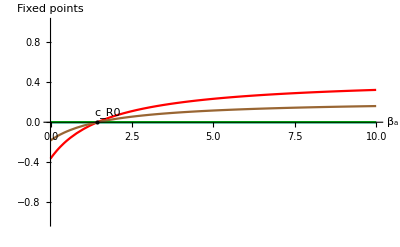

```mathematica
(*Some tests*)
fin=FindInstance[Join[cp,Thread[(var/.so[[2]])>0]],par][[1]];
cN=Drop[fin,{3}];cR0=par[[3]]/.Solve[R0==1,par[[3]]][[1]]; cR0N=cR0/.cN;
fpB=Bifp[mod,cN,inf,par[[3]],0,10,-1,1,cR0N];
fpB[[2]]
```

### Analysis of 3-dim model:

```mathematica
RHS3=Drop[RHS/.cr,-1];//FullSimplify
Print["The 3dim model is", RHS3//MatrixForm]
```

The 3dim model is(-a s β_a-i s β_i+(1-a-i-s) γ_r-s γ_s+Λ-s Λ
i s β_i-a (a_i+a_r-s β_a+Λ)
a a_i-i (γ_i+Λ))

## FHJ graph of SAIR:

In the following we produce the FHJ graph:

```mathematica
groups={{comp[[-1]],comp[[-2]],comp[[-3]],comp[[2]]},{comp[[3]],comp[[4]],comp[[5]],comp[[6]]},{comp[[1]]}}
flow=FHJ[comp,RN,Rv,.5,groups]
Export["SAIRS1gr.pdf",flow]
```

{{R,I,A,S},{A+S,2 A,I+S,A+I},{0}}

SAIRS1gr.pdf

```mathematica
A=Array[a,{2,2}];Ai=Inverse[A];B=Ai.DiagonalMatrix[Array[b,{2}]].A-k IdentityMatrix[2]//Factor;
B//MatrixForm
```

(-(-k a[1,2] a[2,1]+k a[1,1] a[2,2]-a[1,1] a[2,2] b[1]+a[1,2] a[2,1] b[2])/(-a[1,2] a[2,1]+a[1,1] a[2,2]) | -(a[1,2] a[2,2] (b[1]-b[2]))/(a[1,2] a[2,1]-a[1,1] a[2,2])
-(a[1,1] a[2,1] (b[1]-b[2]))/(-a[1,2] a[2,1]+a[1,1] a[2,2]) | -(k a[1,2] a[2,1]-k a[1,1] a[2,2]-a[1,2] a[2,1] b[1]+a[1,1] a[2,2] b[2])/(a[1,2] a[2,1]-a[1,1] a[2,2]))

```mathematica
Print["In the following we dissect the expression of r in order to check its form wrt R0 and check its positivity"]
 nr=Numerator[r/.so[[2]]]; dr=Denominator[r/.so[[2]]];
 Print["the numerator of endemic r is ", nr]
  Print["the Denominator of endemic r is ",dr//FullSimplify]
Print["1-1/R0= ",Together[(1-1/R0)]//FullSimplify]
 (*a check; we already know that the endemic point doesn't exist when R0<1
 Reduce[Join[Thread[(var/.so[[2]])>0],cp,{R0<1}]]*)
```

```mathematica
(*Define Lf as before*)Lf=leiv.{a-ae Log[a],i-ie Log[a]};

(*Define the system dynamics*)
rules={a'[t]->a[t] a[t],i'[t]->i[t] i[t]};  (*Given a'=a a and i'=i i*)

(*Compute the Lie derivative*)
LieDerivative=Dt[Lf,t]/. rules
Lf[a_,i_]:=leiv.{a-ae Log[a],i-ie Log[a]};
LieDerivative=D[Lf[a[t],i[t]],t]/. {a'[t]->a[t] a[t],i'[t]->i[t] i[t]}
```